## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

## Equation and Leaver ansatz

```mathematica
EqTeukolskyAngular=D[((1-x^2) S'[x]), x]+((c x)^2-(m+s x)^2/(1-x^2)+s-2 c s x+A) S[x];
ansatzS={S->Function[x,ⅇ^(c x)((1+x)/2)^km ((1-x)/2)^kp F[x]]};
Ruleκpm={kp->Abs[s+m]/2,km->Abs[s-m]/2};
```

## Rules for handling coefficients

```mathematica
ruleSSjoin={y_z_+w_z_:>Collect[Simplify[y+w],(1+x)^n1_]z,w_ y_z_:>Collect[Simplify[y w],(1+x)^n1_]z};
ruleSSseparate={(y_+w_)z_:>yz+wz};
ruleF={w_. Derivative[n_][F][x]:>w a[p] D[(1+x)^p, {x,n}]pn∞,w_. F[x]:>w a[p] (1+x)^pp0∞};
ruleRemoveM={s^(n_.) m^(k_.):>s^(n-k) (kp^2-km^2)^k/;OddQ[k]&&n≥k,m^n_:>(2 (kp^2+km^2)-s^2)^(n/2)/;EvenQ[n]};
ruleShift[z_]:={z^v_ a[p_] b_.p_i_∞:>z^p a[2 p-v] (b/.{p->2 p-v})pi-p+v∞};
```

## Solve for coefficients

```mathematica
Eq1=(1/(ⅇ^(c x)((1+x)/2)^km ((1-x)/2)^kp) (EqTeukolskyAngular/.ansatzS)//Expand)/.ruleRemoveM/.ruleF//.ruleSSjoin
```

-(-1+p) p (-1+x) (1+x)^(-1+p) a[p]p2∞+-(1+x)^p (-A-c^2+km+km^2+kp+2 km kp+kp^2-s-s^2+2 c (kp+km (-1+x)+x+kp x+s x)) a[p]p0∞+-2 p (1+x)^(-1+p) (kp+km (-1+x)+x+kp x+c (-1+x^2)) a[p]p1∞

```mathematica
Eq2=((Eq1//Simplify)/.{x->𝒰-1}//ExpandAll)//.ruleSSseparate/.ruleShift[𝒰]//.ruleSSjoin//FullSimplify
```

-(-1+p) 𝒰^p (2 c a[-1+p]+p a[p])p2∞+𝒰^p ((A+c^2+2 c (1+2 km+s)-(km+kp-s) (1+km+kp+s)) a[p]+2 (1+2 km) (1+p) a[1+p])p0∞+2 𝒰^p (-c (1+km+kp+s) a[-1+p]+(-1+2 c-km-kp) p a[p]+p (1+p) a[1+p])p1∞

```mathematica
Eq3=With[{maxI=Max[Cases[Eq2,w_p_i_j_->i]]},
Eq2/.w_pi_∞:>∑_(p=i)^(maxI-1) w+wpmaxI∞/;i<maxI
]//.ruleSSjoin//FullSimplify
```

(A+c^2+2 c (1+2 km+s)-(km+kp-s) (1+km+kp+s)) a[0]+2 (1+2 km) a[1]+2 𝒰 (-c (1+km+kp+s) a[0]+2 c a[1]-(1+km+kp) a[1]+2 a[2])+𝒰 ((A+c^2+2 c (1+2 km+s)-(km+kp-s) (1+km+kp+s)) a[1]+4 (1+2 km) a[2])+𝒰^p (-2 c (km+kp+p+s) a[-1+p]+(A+c^2-(km+kp+p-s) (1+km+kp+p+s)+2 c (1+2 km+2 p+s)) a[p]+2 (1+p) (1+2 km+p) a[1+p])p2∞

```mathematica
Eq3/.{z_y_:>z}//Collect[#,{𝒰,𝒰^p},Framed@*FullSimplify]&
```

(A+c^2+2 c (1+2 km+s)-(km+kp-s) (1+km+kp+s)) a[0]+2 (1+2 km) a[1]+𝒰 -2 c (1+km+kp+s) a[0]+c^2 a[1]+2 c (3+2 km+s) a[1]+(A-(1+km+kp-s) (2+km+kp+s)) a[1]+8 (1+km) a[2]+𝒰^p -2 c (km+kp+p+s) a[-1+p]+(A+c^2-(km+kp+p-s) (1+km+kp+p+s)+2 c (1+2 km+2 p+s)) a[p]+2 (1+p) (1+2 km+p) a[1+p]

```mathematica
EqsCoef=-Eq3/.{z_y_:>(z/.{𝒰^p->𝒱})}//CoefficientList[#1,{𝒰,𝒱}]&//Flatten//DeleteCases[#1,0]&//FullSimplify
```

{-(A+c^2+2 c (1+2 km+s)-(km+kp-s) (1+km+kp+s)) a[0]-2 (1+2 km) a[1],2 c (km+kp+p+s) a[-1+p]-(A+c^2-(km+kp+p-s) (1+km+kp+p+s)+2 c (1+2 km+2 p+s)) a[p]-2 (1+p) (1+2 km+p) a[1+p],2 c (1+km+kp+s) a[0]-c^2 a[1]-2 c (3+2 km+s) a[1]+(-A+(1+km+kp-s) (2+km+kp+s)) a[1]-8 (1+km) a[2]}

```mathematica
LeaverCoef={α[p_],β[p_],γ[p_]}->(CoefficientList[EqsCoef⟦2⟧,{a[p+1],a[p],a[p-1]}]⟦Sequence@@#1⟧&)/@Permutations[{2,1,1}]//Thread//Simplify
```

{α[p_]→-2 (1+p) (1+2 km+p),β[p_]→-A-c^2+(km+kp+p-s) (1+km+kp+p+s)-2 c (1+2 km+2 p+s),γ[p_]→2 c (km+kp+p+s)}

```mathematica
And[
α[0]a[1]+β[0]a[0]-EqsCoef[[1]]==0,
a[1+p] α[p]+a[p]β[p]+a[-1+p] γ[p]-EqsCoef[[3]]==0/.p->1
]/.LeaverCoef//Simplify
```

True

## Comparing with the tabled coefficients

```mathematica
recurrSol={ζ[p_]->(ζ[p]/.First[Solve[0=={α[p],β[p],γ[p]}.{ζ[p+1],1,1/ζ[p]},ζ[p]]])};
InvertFraction[r_Integer?Positive][f_]:=Quiet[ReplaceRepeated[f,{EQ[x_,y_/(z_+w_)]:>EQ[w-y/x,-z]/;(!FreeQ[x,β[0]]&&!FreeQ[z,ζ[_]])},MaxIterations->r]];
EigenExpand[n_]=#1/.{EQ[x_,y_]:>EQ@@Normal@Series[{x,y}/.A->∑_(p=0)^(n+1) f[p] c^p,{c,0,n}]}&;
```

```mathematica
R=4;(* R-th inversion *)
P=3;(* Max coef power *)
```

```mathematica
Eq4=Quiet@ReplaceRepeated[EQ[β[0],-a[1]α[0]/a[0]]/.{a[1]->ζ[1],a[0]->1},recurrSol,MaxIterations->8]
Eq5=Eq4//InvertFraction[R]
```

EQ[β[0],(α[0] γ[1])/(β[1]-(α[1] γ[2])/(β[2]-(α[2] γ[3])/(β[3]-(α[3] γ[4])/(β[4]-(α[4] γ[5])/(β[5]-(α[5] γ[6])/(β[6]-(α[6] γ[7])/(β[7]-(α[7] γ[8])/(β[8]+α[8] ζ[9]))))))))]

EQ[β[4]-(α[3] γ[4])/(β[3]-(α[2] γ[3])/(β[2]-(α[1] γ[2])/(β[1]-(α[0] γ[1])/β[0]))),(α[4] γ[5])/(β[5]-(α[5] γ[6])/(β[6]-(α[6] γ[7])/(β[7]-(α[7] γ[8])/(β[8]+α[8] ζ[9]))))]

```mathematica
solCoef=EigenExpand[3][Eq5/.LeaverCoef]//First@Solve[Thread[CoefficientList[Subtract@@#1,c]==0],Evaluate@Table[f[i],{i,0,P}]]&;
```

```mathematica
𝒽[l_]:=((l^2-(kp+km)^2)(l^2-(kp-km)^2)(l^2-s^2))/(2(l^2-1/4)l^3);
EigenCoef={l+l^2-s (1+s),
(-2m s^2)/(l (1+l)),
𝒽[l+1]-𝒽[l]-1,
(2 𝒽[l]m s^2)/((l-1)l^2(l+1))-(2 𝒽[l+1]m s^2)/((l+1)^2 l(l+2)),m^2 s^4((4 𝒽[l+1])/(l^2(l+1)^4(l+2)^2)-(4 𝒽[l])/((l-1)^2(l)^4(l+1)^2))-((l+2)𝒽[l+1]𝒽[l+2])/(2(l+1)(2l+3))+𝒽[l+1]^2/(2(l+1))+(𝒽[l]𝒽[l+1])/(2l(l+1))-𝒽[l]^2/(2 l)+((l-1)𝒽[l-1]𝒽[l])/(2l(2l-1)),
m^3 s^6((8 𝒽[l])/(l^6(l+1)^3(l-1)^3)-(8 𝒽[l+1])/((l)^3(l+1)^6(l+2)^3))+m s^2 𝒽[l](-(𝒽[l+1](7 l^2+7l+4))/(l^3(l+2)(l+1)^3(l-1))-(𝒽[l-1](3l-4))/(l^3(l+1)(2 l-1)(l-2)))+m s^2(((3l+7)𝒽[l+1]𝒽[l+2])/(l(l+1)^3(l+3)(2l+3))-(3 𝒽[l+1]^2)/(l(l+1)^3(l+2))+(3 𝒽[l]^2)/((l-1)(l)^3(l+1))),
(16 m^4 s^8)/(l^4(l+1)^4)(𝒽[l+1]/((l+2)^4(l+1)^4)-𝒽[l]/(l^4(l-1)^4))+(4 m^2 s^4)/(l^2(l+1)^2)(-((3 l^2+14l+17)𝒽[l+1]𝒽[l+2])/((l+1)^3(l+2)(l+3)^2(2l+3))+(3 𝒽[l+1]^2)/((l+1)^3(l+2)^2)-(3 𝒽[l]^2)/(l^3(l-1)^2)+((11 l^4+22 l^3+31 l^2+20l+6)𝒽[l]𝒽[l+1])/((l+1)^3(l+2)(l+3)^2(2l+3))+((3 l^2-8l+6)𝒽[l]𝒽[l-1])/(l^3(l-2)^2(l-1)(2l-1)))+(𝒽[l+1]𝒽[l+2])/(4(l+1)(2l+3)^2)(((l+3)𝒽[l+3])/3+(l+2)/(l+1)((l+2)𝒽[l+2]-(7l+10)𝒽[l+1]+((3 l^2+2l-3)𝒽[l])/l))+𝒽[l+1]^3/(2(l+1)^2)-𝒽[l]^3/(2 l^2)+(𝒽[l]𝒽[l+1])/(4 l^2(l+1)^2)((2 l^2+4l+3)𝒽[l]-(2 l^2+1)𝒽[l+1]-((l^2-1)(3 l^2+4l-2)𝒽[l-1])/(2l-1)^2)+
(𝒽[l-1]𝒽[l])/(4 l^2(2l-1)^2)((l-1)(7l-3)𝒽[l]-(l-1)^2 𝒽[l-1]-(l(l-2)𝒽[l-2])/3)
};
```

```mathematica
(EigenCoef[[;;P+1]]==Table[f[i],{i,0,P}]/.solCoef)//(Expand[#/.{l->R+km+kp}]/.ruleRemoveM)&//Simplify
```

True

## Leaver’s method for calculating eigenvalues

```mathematica
Clear@EigenLeaver
EigenLeaver[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real?Negative,M_Integer:150]:=EigenLeaver[𝓈,ℓ,-𝓂,-𝒸,M]
EigenLeaver[𝓈_Integer?Negative,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real,M_Integer:150]:=EigenLeaver[-𝓈,ℓ,𝓂,𝒸,M]
EigenLeaver[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real,M_Integer:150]/;(ℓ≥Max[Abs[𝓈],Abs[𝓂]]):=
(𝓈(𝓈+1)+A)/.Quiet@FindRoot[Fold[(β[#2-1]-(α[#2-1]γ[#2])/#1)&,1,Reverse@Range[M]]/.(LeaverCoef/.Ruleκpm/.{m->𝓂,l->ℓ,s->𝓈,c->𝒸}),{A,Table[c^(i-1),{i,Length@EigenCoef}].Simplify[EigenCoef/.Ruleκpm/.{m->𝓂,s->𝓈}]/.{l->ℓ,c->𝒸}}]
```

```mathematica
GetListEigenLeaver[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸Max_Real,M_Integer:150]/;(ℓ≥Max[Abs[𝓈],Abs[𝓂]]):=Block[{data=Table[{c,ℓ(ℓ+1)},{c,-𝒸Max,𝒸Max,0.01}]},
(data⟦#+1,2⟧=(𝓈(𝓈+1)+A)/.Quiet@FindRoot[Fold[(β[#2-1]-(α[#2-1]γ[#2])/#1&),1,Reverse@Range[M]]/.(LeaverCoef/.Ruleκpm/.{m->𝓂,l->ℓ,s->𝓈,c->data⟦#+1,1⟧}),{A,data⟦#,2⟧-𝓈(𝓈+1)}])&/@Range[Length@data-1];
data
];
```

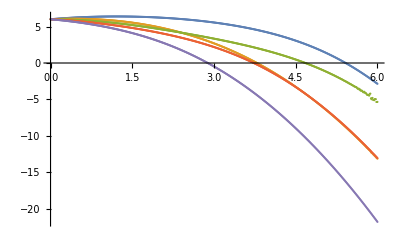

```mathematica
list1//ListPlot
```

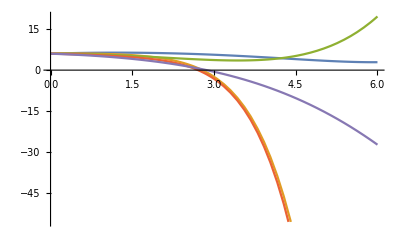

```mathematica
Plot[ParallelTable[Table[c^(i-1),{i,Length@EigenCoef}].Simplify[EigenCoef/.Ruleκpm/.{m->𝓂,s->-1}]/.{l->2},{𝓂,-2,2}]//Evaluate,{c,0,6}]
```

```mathematica
Quiet@CreateDirectory["Definitions"];
DeleteFile["Definitions/Eigenvalues.wl"]
Save["Definitions/Eigenvalues.wl",{𝒽,LeaverCoef,EigenCoef,Ruleκpm,EigenLeaver}]
```

```mathematica
Import@GetSWSHEigenFile[1,1,1]
```

Import::nffil: File not found during Import.

```mathematica
Table[Export[GetSWSHEigenFile[1,l,m],GetListEigenLeaver[1,l,m,3.001]],{l,{3}},{m,-l,l}]
```

{{Data/SWSH-Eigenvalues/SWSH_EV_1_3_-3.csv,Data/SWSH-Eigenvalues/SWSH_EV_1_3_-2.csv,Data/SWSH-Eigenvalues/SWSH_EV_1_3_-1.csv,Data/SWSH-Eigenvalues/SWSH_EV_1_3_0.csv,Data/SWSH-Eigenvalues/SWSH_EV_1_3_1.csv,Data/SWSH-Eigenvalues/SWSH_EV_1_3_2.csv,Data/SWSH-Eigenvalues/SWSH_EV_1_3_3.csv}}

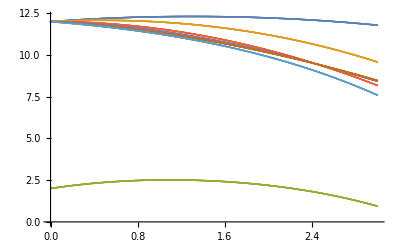

```mathematica
Import@GetSWSHEigenFile[1,3,#]&/@Range[-3,3]//ListPlot
```

## Numerical relaxation method (ongoing)

### Solution to c=0

```mathematica
SpinWeightedSphericalHarmonicsY[s_,ℓ_,m_,θ_,ϕ_]:=(-1)^(m+ℓ-s) √(((1+2 ℓ) (-m+ℓ)! (m+ℓ)!)/(4 π (-s+ℓ)! (s+ℓ)!)) Sin[θ/2]^(2 ℓ) Inactive[Sum][ (-1)^-r ⅇ^(ⅈ m ϕ) Binomial[-s+ℓ,r] Binomial[s+ℓ,-m+r+s] Cot[θ/2]^(-m+2 r+s),{r,0,-s+ℓ}]
```

```mathematica
(EqTeukolskyAngular/.c->0)/.{S->Function[x,Activate@SpinWeightedSphericalHarmonicsY[s,l,m,ArcCos[x],0]//FunctionExpand//Evaluate]}//Expand//PowerExpand//Simplify//FullSimplify//Solve[#==0,A]&
```

{{A→(l-s) (1+l+s)}}

### Limit x→±1 of (1-x)^kp(1+x)^km Y_(s,l,m)(x)

```mathematica
SWHexpanded=PowerExpand[FunctionExpand[(1-x)^-kp (1+x)^-km SpinWeightedSphericalHarmonicsY[s,ℓ,m,ArcCos[x],0]]]//.{(1-x)^α_ (1+x)^β_ z_w_:>PowerExpand[z (1-x)^α (1+x)^β]w,z_ y_w_:>y zw/;FreeQ[y,r]}
```

1/(√π)(-1)^(m-s+ℓ) 2^(-1-ℓ) √(1+2 ℓ) √Gamma[1-m+ℓ] √Gamma[1+m+ℓ] √Gamma[1-s+ℓ] √Gamma[1+s+ℓ] ((-1)^-r (1-x)^(-kp+1/2 (m-2 r-s)+ℓ) (1+x)^(-km+1/2 (-m+2 r+s)))/(Gamma[1+r] Gamma[1-m+r+s] Gamma[1+m-r+ℓ] Gamma[1-r-s+ℓ])r0-s+ℓ

```mathematica
{rP,rM}=Cases[SWHexpanded,(1-# x)^α_:>Solve[α==0,r]⟦1,1⟧,∞]/.Ruleκpm&/@{1,-1}
```

{{r→1/2 (m-s+2 ℓ-Abs[m+s])},{r→1/2 (m-s+Abs[-m+s])}}

```mathematica
$Assumptions={{s,ℓ,m}∈Integers,ℓ≥Max[Abs@s,Abs@m],ℓ≥Abs[s],ℓ≥Abs[m],x∈Reals};
{BCp,BCm}=FullSimplify[PiecewiseExpand[FullSimplify[PowerExpand[SWHexpanded/.Ruleκpm/.{z_w_:>(z/.#1)}]]/.{x->#2}]]&@@@{{rP,1},{rM,-1}}
$Assumptions={};
```

{Piecewise[{{((-1)^m 2^(-1-m) √(((1+2 ℓ) (m+ℓ)! (s+ℓ)!)/((-m+ℓ)! (-s+ℓ)!)))/(√π (m+s)!), m≥s&&m+s≥0}, {((-1)^m 2^(-1-s) √(((1+2 ℓ) (m+ℓ)! (s+ℓ)!)/((-m+ℓ)! (-s+ℓ)!)))/(√π (m+s)!), m+s≥0}, {((-1)^s 2^(-1+s) √(((1+2 ℓ) (-m+ℓ)! (-s+ℓ)!)/((m+ℓ)! (s+ℓ)!)))/(√π (-m-s)!), m≥s&&m+s<0}, {((-1)^s 2^(-1+m) √(((1+2 ℓ) (-m+ℓ)! (-s+ℓ)!)/((m+ℓ)! (s+ℓ)!)))/(√π (-m-s)!), True}}],Piecewise[{{((-1)^ℓ 2^(-1-m) √((1+2 ℓ) (m+ℓ)! (-s+ℓ)!))/(√π (m-s)! √((-m+ℓ)! (s+ℓ)!)), m≥s&&m+s≥0}, {((-1)^ℓ 2^(-1+s) √((1+2 ℓ) (m+ℓ)! (-s+ℓ)!))/(√π (m-s)! √((-m+ℓ)! (s+ℓ)!)), m≥s}, {((-1)^(m+s+ℓ) 2^(-1-s) √((1+2 ℓ) (-m+ℓ)! (s+ℓ)!))/(√π (-m+s)! √((m+ℓ)! (-s+ℓ)!)), m+s≥0&&m<s}, {((-1)^(m+s+ℓ) 2^(-1+m) √((1+2 ℓ) (-m+ℓ)! (s+ℓ)!))/(√π (-m+s)! √((m+ℓ)! (-s+ℓ)!)), True}}]}

### z_slm’[x]/z_slm[x] ratio at x=±1

```mathematica
ansatzSNum={S->Function[x,(1+x)^km (1-x)^kp F[x]]};
ansatzFp={F->Function[x,Sum[a[i](1-x)^i,{i,0,3}]]};
ansatzFm={F->Function[x,Sum[a[i](1+x)^i,{i,0,3}]]};
```

```mathematica
FullSimplify[a[1]/a[0]/.First@Solve[Normal@Series[Expand[(EqTeukolskyAngular/.ansatzSNum/.#1)/((1-x)^kp (1+x)^km)]//.ruleRemoveM,{x,#2,0}]==0,a[1]]]&@@@{{ansatzFm,-1},{ansatzFp,+1}}
```

{-(A+c^2+2 c s-(km+kp-s) (1+km+kp+s))/(2+4 km),-(A+c^2-2 c s-(km+kp-s) (1+km+kp+s))/(2+4 kp)}

### S_(n,m) matrix

```mathematica
ruleFDE={F''[x]->(𝔜[1,k]-𝔜[1,k-1])/h,F'[x]->(𝔜[1,k]+𝔜[1,k-1])/2,F[x]->(𝔜[0,k]+𝔜[0,k-1])/2,A->(𝔜[2,k]+𝔜[2,k-1])/2,x->(x[k]+x[k-1])/2};
```

```mathematica
Clear@𝔈;Clear@M;
𝔈[0,k_]=(𝔜[0,k]-𝔜[0,k-1]-h(𝔜[1,k]+𝔜[1,k-1])/2);
𝔈[1,k_]=Simplify[Expand[h(EqTeukolskyAngular/.ansatzSNum)/((1-x)^(1+kp) (1+x)^(1+km))]//.ruleRemoveM]/.ruleFDE//Collect[#, 𝔜[__],FullSimplify]&;
𝔈[2,k_]=𝔜[2,k]-𝔜[2,k-1];
𝔈[2,0]=𝔜[1,0]-𝔜[0,0]((-4𝔜[2,0]-4 c^2+4km+4 km^2+m^2-4s-8c s+2 m s-3 s^2)/(16km+8 km^2-2(-4+m^2-2m s+s^2))+kp/2)//Collect[#1//.ruleRemoveM,𝔜[__],FullSimplify]&;
𝔈[0,M-1]=𝔜[1,M-1]-𝔜[0,M-1] ((4 𝔜[2,M-1]+4 c^2-4 km-4 km^2-m^2+4 s-8 c s+2 m s+3 s^2)/(16 kp+8 kp^2-2 (-4+m^2+2 m s+s^2))-km/2)//Collect[#1//.ruleRemoveM,𝔜[__],FullSimplify]&;
𝔈[1,M-1]=𝔜[0,M-1]-γ;
```

```mathematica
D𝔈[a_,b_,k_]:=FullSimplify[D[{𝔈[0,k],𝔈[1,k],𝔈[2,k]}, {{𝔜[0,k-1],𝔜[1,k-1],𝔜[2,k-1],𝔜[0,k],𝔜[1,k],𝔜[2,k]}}]/.ruleRemoveM//.{α_. x[-1+k]+α_. x[k]->2 α x̃[k],α_. 𝔜[j_,-1+k]+α_. 𝔜[j_,k]->2 α 𝔜̃[j,k]}]⟦a+1,b+1⟧;
```

```mathematica
D𝔈[1,{0,1,2,3,4,5},k]
```

{(h ((km+kp-s) (1+km+kp+s)+c x̃[k] (2 s-c x̃[k])-𝔜̃[2,k]))/(2 (-1+(x̃[k])^2)),-1+(h (-km+kp+(1+km+kp) x̃[k]))/(-1+(x̃[k])^2),(h 𝔜̃[0,k])/(2-2 (x̃[k])^2),(h ((km+kp-s) (1+km+kp+s)+c x̃[k] (2 s-c x̃[k])-𝔜̃[2,k]))/(2 (-1+(x̃[k])^2)),1+(h (-km+kp+(1+km+kp) x̃[k]))/(-1+(x̃[k])^2),(h 𝔜̃[0,k])/(2-2 (x̃[k])^2)}